```mathematica
(* Initialisation *)
(* Evaluate before starting writing "real code" *)
(* Usage e.g.: "ld [Spacekey]" becomes "⊨", so writing "a ld 5" turns into "a⊨5" *) 
SetOptions[EvaluationNotebook[], 
			 InputAutoReplacements -> { (* special AceGen assignment operators: *) "ld"-> "⊨","ls"->"⊢","rd"->"⫤","rs"->"⊣",
					                                 (* brackets and symbols: *) "dbl"->"⟦","dbr"->"⟧","lcb"->"{","rcb"->"}","lsb"->"[","rsb"->"]","->"->"→",
					                                 (* shortcuts for starting/ending a comment block: *) "co"->"(*","cc"->"*)"
					                              }
		   ]
(* Output the current time, so we know when AceGen has been executed the last time *)
Now
```

Thu 9 May 2024 17:19:59GMT+2

```mathematica
(* Clear all old variables initially to have a fresh start *)
ClearAll["Global`*"] 
(* Start AceGen *) 
<<AceGen`;
Needs["AceTensorFunctions`"]; 

NAME = "Step3";
SMSInitialize[NAME,"Language"-> "Matlab","Mode"-> "Optimal"]; 

(* Define the maximum number of Newton-Raphson iterations, as this also defines the size of convergenceHistory$$ *) 
n iterations = 20;

(* Start a module, which represents the to be created function, with name "NAME" and the specified input and output arguments *) 
SMSModule[NAME,Real[ displacement$$, parameter$$, convergedValue$$, convergenceHistory$$[2,n iterations] ],
		"Input"-> { displacement$$, parameter$$ },
		"Output" -> { convergedValue$$, convergenceHistory$$ }
	       ];
displacement ⊨ SMSReal[ displacement$$ ];
parameter ⊨ SMSReal[ parameter$$ ];
```

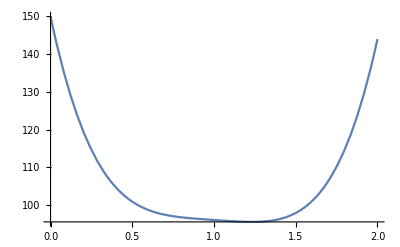

```mathematica
(* Define some energy function and plot it with an exemplary parameter=1 *) 
W energy[utmp_,parameter_]:=( 1/2 * 100 * (utmp-parameter)^4+utmp^2 -5utmp+100);
Plot[W energy[x,1],{x,0,2}]
```

```mathematica
u tmp ⫤ displacement;
SMSDo[i NR,1,n iterations,1,{u tmp}];
         (* Compute the energy to be minimised using the variable u tmp *) 
	W ⊨ W energy[u tmp,parameter];
         (* Find the mininum of the energy W by computing the slope of the energy which will be iteratively computed to find the minimum (R=0) *) 
	R ⊨ SMSD[W,u tmp];
         (* Give some output on the progress and export it to convergenceHistory$$ *) 
         SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
         SMSExport[u tmp,convergenceHistory$$[i NR,1]];
         SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
         (* Check for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ];
                  (* If converged, export the current value of u tmp *) 
		SMSExport[u tmp,convergedValue$$];
		SMSPrintMessage["converged"];
                  (* Leave the SMSDo-Loop *) 
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iteration is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSExport[u tmp,convergedValue$$];
		SMSPrintMessage["failed"];
		SMSBreak[];
          SMSEndIf[];
          (* Compute the derivative and update the value of u tmp *) 
	dRdu ⊨ SMSD[R, u tmp];
	u tmp  ⊣ u tmp - 1/dRdu * R;
SMSEndDo[];
```

```mathematica
(* #1 Wrong because ...
SMSDo[i NR,1,10,1,displacement];
	W ⊨ 1/2 * 100 * (displacement-parameter)^2+100;
	R ⊨ SMSD[W,displacement];
	SMSIf[ SMSAbs[R]<1*^-8 ];
		SMSExport[displacement,update$$];
		SMSPrintMessage["converged"];
		SMSBreak[];
	SMSEndIf[];
	dRdu ⊨ SMSD[R, displacement];
	displacement  ⊢ displacement - 1/dRdu * R;
SMSEndDo[]; *) 
(* #2 Wrong because ...
*) 
(* @todo Add more cases and explanations as there are many ways to do it wrong here *)
```

```mathematica
(* Output the time at the end of the execution *)
Now 
(* Write output file containing all the above defined functions introduced by SMSModule *)
(* Create output file named "NAME", '"LocalAuxiliaryVariables" -> True' is a command to exclude the AceGen internal array "v" from the list of input and output arguments of the created subroutine *)
SMSWrite[NAME,"LocalAuxiliaryVariables" -> True]; 
(* Print the content of the just created file on screen (sensible only for small file sizes) *)
FilePrint[ StringJoin[NAME,Which[SMSLanguage=="Fortran",".f",
							   SMSLanguage=="Matlab",".m",
							   SMSLanguage=="C++",".cpp",
							   SMSLanguage=="C",".c"
							 ]
					]
		   ]
```

Thu 9 May 2024 17:19:59GMT+2

File: Step3.m  Size: 1665  Time: 1
Method | Step3
No.Formulae | 13
No.Leafs | 136

%**************************************************************
%* AceGen    7.505 Linux (16 Aug 22)                          *
%*           Co. J. Korelc  2020           9 May 24 17:20:00  *
%**************************************************************
% User     : Full professional version
% Notebook : AceGen-SMSDo
% Evaluation time                 : 1 s     Mode  : Optimal
% Number of formulae              : 13      Method: Automatic
% Subroutine                      : Step3 size: 136
% Total size of Mathematica  code : 136 subexpressions
% Total size of Matlab code      : 777 bytes 

%*********************** F U N C T I O N **************************
function[convergedValue,convergenceHistory]=Step3(displacement,parameter);
persistent v;
if size(v)<140
  v=zeros(140,'double');
end;
v(3)=displacement;
for i4=1:1:20;
 v(6)=-parameter+v(3);
 v(7)=-5e0+2e0*v(3)+200e0*Power(v(6),3);
 disp(sprintf("\n%s %f %s %f %s %f %s %f ","iteration i_NR=",i4,": W=",100e0-5e0*v(3)+(v(3)*v(3)) ...
  +50e0*Power(v(6),4),"; R=",v(7),"; SMSAbs[R]=",abs(v(7))));
 convergenceHistory(i4,1)=v(3);
 convergenceHistory(i4,2)=abs(v(7));
 if(abs(v(7))<0.1e-7)
  convergedValue=v(3);
  disp(sprintf("\n%s ","converged"));
  break;
 else;
 end;
 if(i4>=20)
  convergedValue=v(3);
  disp(sprintf("\n%s ","failed"));
  break;
 else;
 end;
 v(3)=v(3)-v(7)/(2e0+600e0*(v(6)*v(6)));
end;


function [x]=SMSKDelta(i,j)

if (i==j) , x=1; else x=0; end;

end

function [x]=SMSDeltaPart(a,i,j,k)

l=round(i/j);

if (mod(i,j) ~= 0 | l>k) , x=0; else x=a(l); end;

end

function [x]=Power(a,b)

x=a^b;

end

function [x]=SMSTernaryOperator(a,b,c)

if (c) , x=a; else x=b; end;

end

end